## ldev 1*L0

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=1;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=-0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.2,0.8,(0.8-0.2)/30}];
gtil=Table[γ,{γ,0.0001,0.1,(0.1-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
tfF=Table[Table[AllTrue[conditions1[[q,p]],#==True&],{p,1,nE2}],{q,1,nE3}];
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

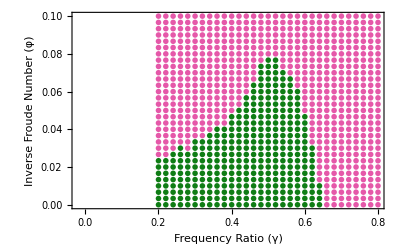

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.1}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;



Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=1;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);


ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]]===True,{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

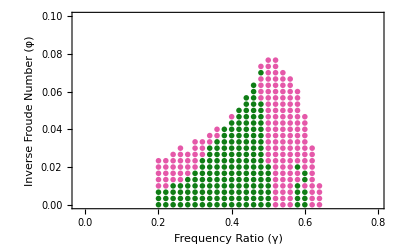

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.1}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=50;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
ratio=1;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[p]][[;;1]]==={True},{p,1,nE2}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

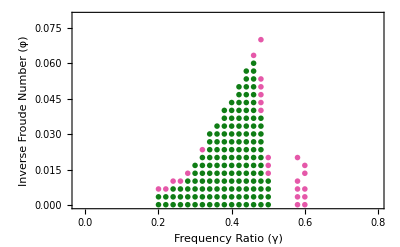

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]],Style[falsepoints4,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=200;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=-0;
ratio=1;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[p]][[;;2]]==={True,True},{p,1,nE2}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

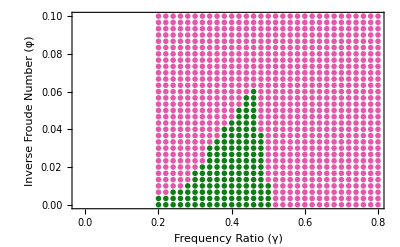

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.1}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev1TP.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev1FP.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
```

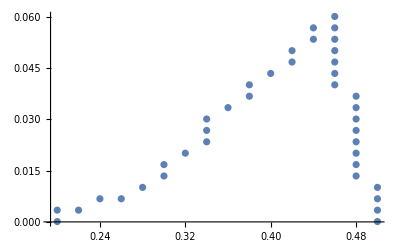

```mathematica
groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];

sortV=Values@GroupBy[SortBy[filterbase,First],First];
perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-(0.06-0.0001)/30]<10^-6&],{i,1,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Table[Mean[inbetw[[i]]],{i,1,Length[inbetw]}];
perfect2=DeleteDuplicates[Join[perfectpoints]];
ListPlot[perfect2,PlotRange->All]
```

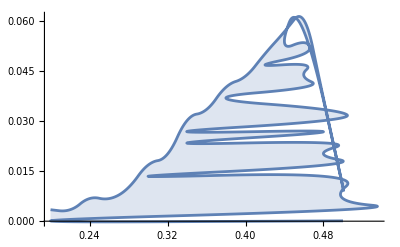

```mathematica
grouped=GatherBy[Round[perfect2,0.000001],First];

keptList=First[SortBy[#,-Last[#]&]]&/@grouped;
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
perfect3=If[Last[keptList][[2]]>Last[droppedList][[2]],Join[keptList,droppedList],Append[DeleteCases[Join[keptList,droppedList],Last[keptList]],Last[keptList]]](*this is to remove the point last point and then placing it at the end sometimes it is not sorted rightly*);
ListLinePlot[{perfect3},PlotRange->All,Filling->Axis,InterpolationOrder->2]
```

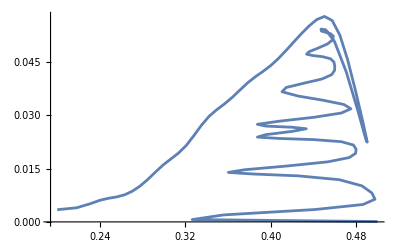

```mathematica
ListLinePlot[BSplineFunction[perfect3]/@Subdivide[0,1,100]]
```

```mathematica
ListPlot[perfect3]
```

-Graphics-

## ldev 1.5

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=1.5;
l00=1;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.01,0.6,(0.6-0.01)/30}];
gtil=Table[γ,{γ,0.0001,0.08,(0.08-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
tfF=Table[Table[AllTrue[conditions1[[q,p]],#==True&],{p,1,nE2}],{q,1,nE3}];
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

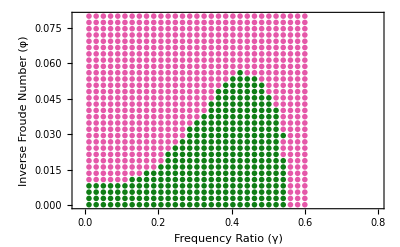

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}],

Plot[{p21},{m,0.23,2},PlotStyle->ColorData["Rainbow",0],PlotRange->{All,{0,2}}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

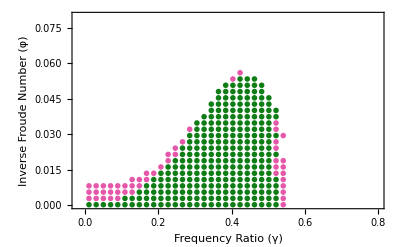

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=50;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=1.5;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;1]]=={True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

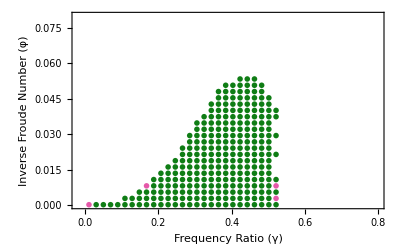

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]],Style[falsepoints4,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=300;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i]]=={True,True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

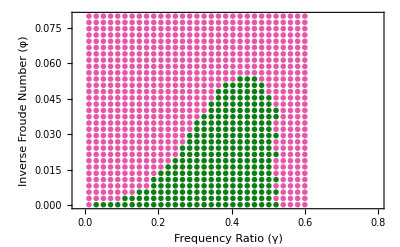

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15FP.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
```

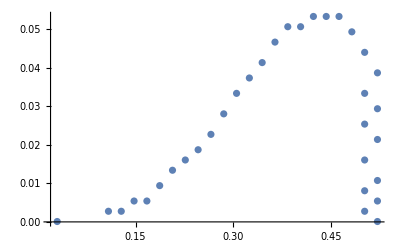

```mathematica
groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];

sortV=Values@GroupBy[SortBy[filterbase,First],First];
perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-(0.08-0.0001)/30]<10^-6&],{i,1,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Table[Mean[inbetw[[i]]],{i,1,Length[inbetw]}];
perfect2=DeleteDuplicates[Join[perfectpoints]];
ListPlot[perfect2,PlotRange->All]
```

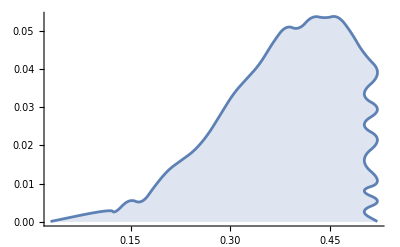

```mathematica
grouped=GatherBy[Round[perfect2,0.000001],First];

keptList=First[SortBy[#,-Last[#]&]]&/@grouped;
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
perfect3=Join[keptList,droppedList];
ListLinePlot[{perfect3},PlotRange->All,Filling->Axis,InterpolationOrder->2]
```

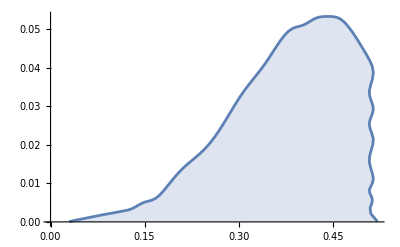

```mathematica
points=Join[BSplineFunction[perfect3]/@Subdivide[0,1,100]];
ListLinePlot[points,Filling->Axis]
```

## ldev 2

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=2;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.01,0.6,(0.6-0.01)/30}];
gtil=Table[γ,{γ,0.0001,0.08,(0.08-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
(0.08-0.0001)/30
```

0.00266333

```mathematica
inty
```

{0.00266333}

```mathematica
0.002663333333333333
0.002663333333333333
```

0.00266333

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

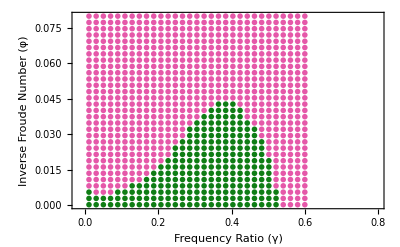

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
ratio=2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

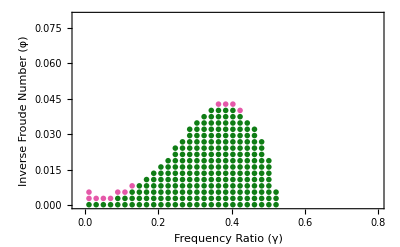

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=40;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=2;
Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

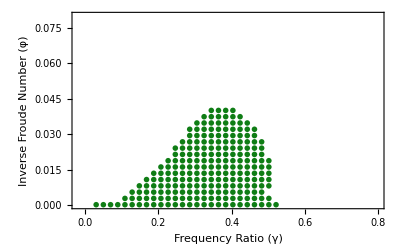

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]](*,Style[falsepoints4,ColorData["FruitPunchColors",0.9]]*)},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=250;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
ratio=2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

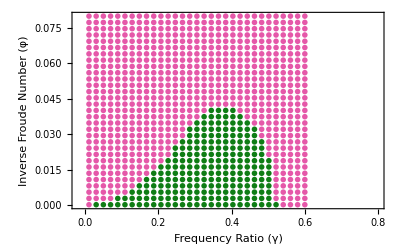

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev2TP.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev2FP.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
inty=Commonest[Differences[Flatten[Select[Gather[Flatten[Last[groupedVpoints]]],Length[#]==1&]]]][[1]];
```

```mathematica
groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];

sortV=Values@GroupBy[SortBy[filterbase,First],First];
perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-inty]<10^-3&],{i,1,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Table[Mean[inbetw[[i]]],{i,1,Length[inbetw]}];
perfect2=DeleteDuplicates[Join[perfectpoints]];
```

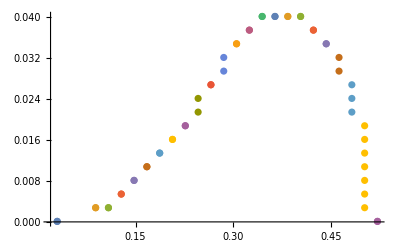

```mathematica
ListPlot[sortV,PlotRange->All]
```

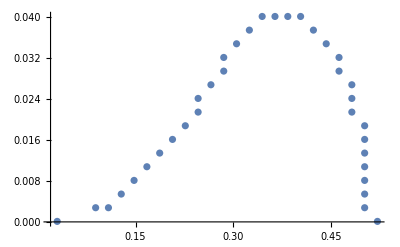

```mathematica
ListPlot[perfect2,PlotRange->All]
```

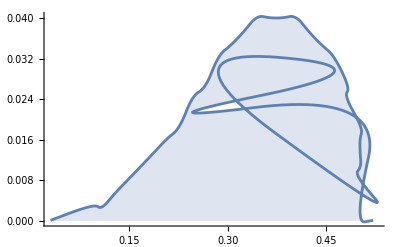

```mathematica
grouped=GatherBy[Round[perfect2,0.000001],First];
sortedgroup=SortBy[#,-Last[#]&]&/@grouped;

keptList=(*First[SortBy[#,-Last[#]&]]&/@grouped;*)Flatten[Table[If[Length[sortedgroup[[i]]]>1,Most[sortedgroup[[i]]],sortedgroup[[i]]],{i,1,Length[sortedgroup]}],1];
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
perfect3I=If[droppedList=!={}&&Last[keptList][[2]]>Last[droppedList][[2]],Join[keptList,droppedList],Append[DeleteCases[Join[keptList,droppedList],Last[keptList]],Last[keptList]]];
perfect3=DeleteDuplicates[DeleteCases[perfect3I,{Max[Map[First,perfect3I]],x_}/;x>0.0001]];
ListLinePlot[{perfect3},PlotRange->All,Filling->Axis,InterpolationOrder->2]
```

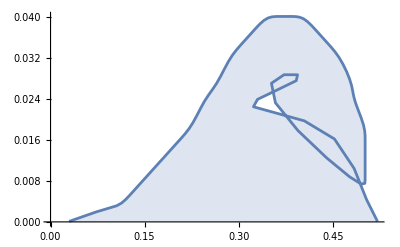

```mathematica
points=Join[BSplineFunction[perfect3]/@Subdivide[0,1,100]];
ListLinePlot[points,Filling->Axis]
```

## ldev 2.5

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=2.5;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.01,0.6,(0.6-0.01)/30}];
gtil=Table[γ,{γ,0.0001,0.08,(0.08-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
(0.08-0.0001)/30
```

0.00266333

```mathematica
inty
```

{0.00266333}

```mathematica
0.002663333333333333
0.002663333333333333
```

0.00266333

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

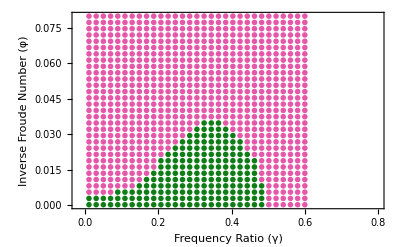

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
ratio=2.5;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

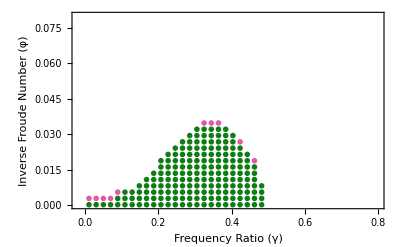

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=40;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=2.5;
Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

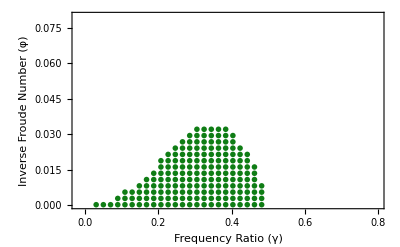

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]](*,Style[falsepoints4,ColorData["FruitPunchColors",0.9]]*)},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=250;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
ratio=2.5;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

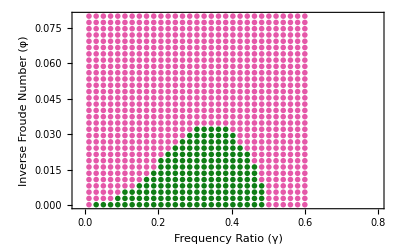

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev25TP.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev25FP.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
inty=Commonest[Differences[Flatten[Select[Gather[Flatten[Last[groupedVpoints]]],Length[#]==1&]]]][[1]];
```

```mathematica
groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];

sortV=Values@GroupBy[SortBy[filterbase,First],First];
perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-inty]<10^-3&],{i,1,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Table[Mean[inbetw[[i]]],{i,1,Length[inbetw]}];
perfect2=DeleteDuplicates[Join[perfectpoints]];
```

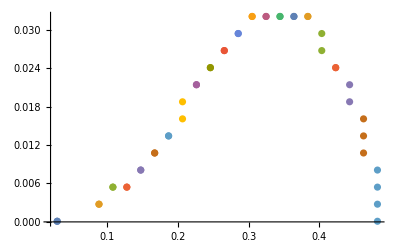

```mathematica
ListPlot[sortV,PlotRange->All]
```

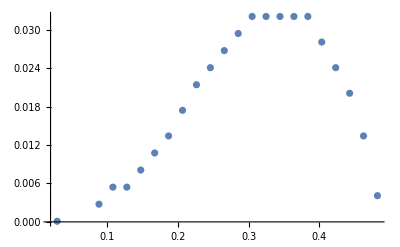

```mathematica
ListPlot[perfect2,PlotRange->All]
```

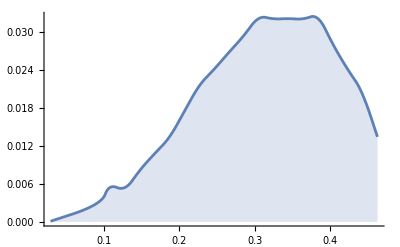

```mathematica
grouped=GatherBy[Round[perfect2,0.000001],First];
sortedgroup=SortBy[#,-Last[#]&]&/@grouped;

keptList=(*First[SortBy[#,-Last[#]&]]&/@grouped;*)Flatten[Table[If[Length[sortedgroup[[i]]]>1,Most[sortedgroup[[i]]],sortedgroup[[i]]],{i,1,Length[sortedgroup]}],1];
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
perfect3I=If[droppedList=!={}&&Last[keptList][[2]]>Last[droppedList][[2]],Join[keptList,droppedList],Append[DeleteCases[Join[keptList,droppedList],Last[keptList]],Last[keptList]]];
perfect3=DeleteDuplicates[DeleteCases[perfect3I,{Max[Map[First,perfect3I]],x_}/;x>0.0001]];
ListLinePlot[{perfect3},PlotRange->All,Filling->Axis,InterpolationOrder->2]
```

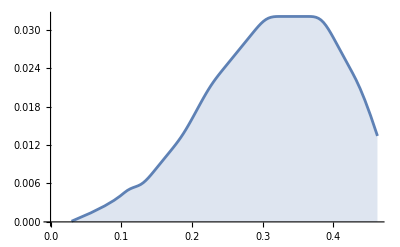

```mathematica
points=Join[BSplineFunction[perfect3]/@Subdivide[0,1,100]];
ListLinePlot[points,Filling->Axis]
```

## ldev 3

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;
l00=1;
ratio=3;
Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.025,0.6,(0.6-0.025)/30}];
gtil=Table[γ,{γ,0.0001,0.06,(0.06-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

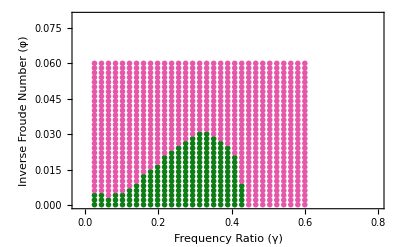

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=3;
Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

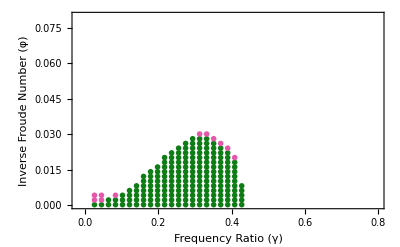

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=40;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=3;
Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

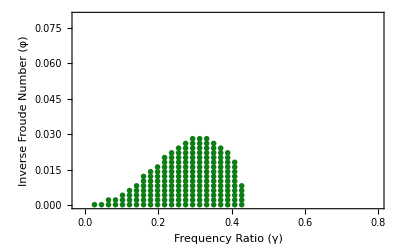

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]](*,Style[falsepoints4,ColorData["FruitPunchColors",0.9]]*)},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=250;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;
ratio=3;
Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->ratio*l00,l0->l00,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

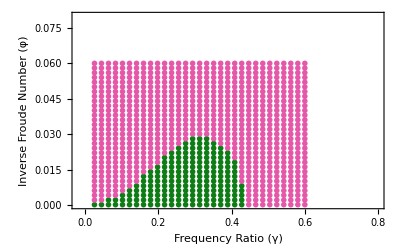

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev3TP.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev3FP.mx",finalfalsepoints];
```

```mathematica
groupedHpoints=Values@GroupBy[SortBy[finaltruepoints,Last](*Sorting the points according to ascending order of second element*),#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[finaltruepoints,First](*Sorting the points according to ascending order of second element*),#[[1]]&];
listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,1,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,1,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates[Join[listHbound,listVbound]];
```

```mathematica
groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];

sortV=Values@GroupBy[SortBy[filterbase,First],First];
perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-(0.06-0.0001)/30]<10^-6&],{i,1,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Table[Mean[inbetw[[i]]],{i,1,Length[inbetw]}];
perfect2=DeleteDuplicates[Join[perfectpoints]];
```

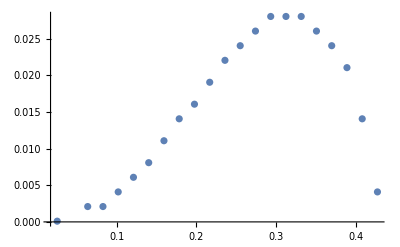

```mathematica
ListPlot[perfect2,PlotRange->All]
```

```mathematica
perfect3I
```

perfect3I

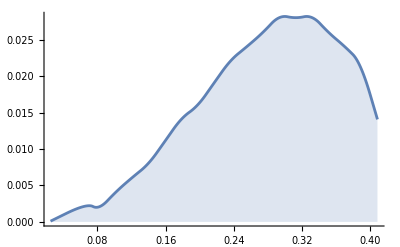

```mathematica
grouped=GatherBy[Round[perfect2,0.000001],First];
sortedgroup=SortBy[#,-Last[#]&]&/@grouped;

keptList=(*First[SortBy[#,-Last[#]&]]&/@grouped;*)Flatten[Table[If[Length[sortedgroup[[i]]]>1,Rest[sortedgroup[[i]]],sortedgroup[[i]]],{i,1,Length[sortedgroup]}],1];
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
perfect3I=If[droppedList=!={}&&Last[keptList][[2]]>Last[droppedList][[2]],Join[keptList,droppedList],Append[DeleteCases[Join[keptList,droppedList],Last[keptList]],Last[keptList]]];
perfect3=DeleteDuplicates[DeleteCases[perfect3I,{Max[Map[First,perfect3I]],x_}/;x>0.0001]];
ListLinePlot[{perfect3},PlotRange->All,Filling->Axis,InterpolationOrder->2]
```

```mathematica
(*distancelist=Table[Table[EuclideanDistance[perfect3[[i]],perfect3[[j]]],{i,1,Length[perfect3]}],{j,1,Length[perfect3]}];*)
```

```mathematica
(*visited={1};
Do[Module[{current,done},current=i;
done=Flatten[Position[distancelist[[i]],Min[Delete[distancelist[[i]],List/@visited]]]];
visited=Flatten[Append[visited,done]]; 
    ],{i,1,n}   (*n-1 steps needed since one point is already visited*)];*)
```

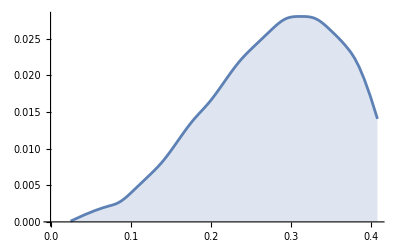

```mathematica
points=Join[BSplineFunction[perfect3]/@Subdivide[0,1,100]];
ListLinePlot[points,Filling->Axis]
```

## Combine plots

```mathematica
ldev1=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev1TP.mx"];(*becauise in this file l0 is 1.2*)
ldev2=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofztD0008TP.mx"];
ldev25=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev25TP.mx"];
ldev3=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev3TP.mx"];
```

```mathematica
processPoints[z012_]:=Module[{groupedHpoints,groupedVpoints,listHbound,listVbound,boundarypoints,groupfilter,filterbase,inty,sortV,perfectsplit,inbetw,perfectpoints,perfect2,grouped,sortedgroup,keptList,droppedList,perfect3I,perfect3,points4},(*Step 1:Group and sort by Y (2nd coord) and X (1st coord)*)groupedHpoints=Values@GroupBy[SortBy[z012,Last],#[[2]]&];
groupedVpoints=Values@GroupBy[SortBy[z012,First],#[[1]]&];
(*Step 2:Create horizontal and vertical boundary point pairs*)listHbound=Flatten[Table[{First[groupedHpoints[[i]]],Last[groupedHpoints[[i]]]},{i,Length[groupedHpoints]}],1];
listVbound=Flatten[Table[{First[groupedVpoints[[i]]],Last[groupedVpoints[[i]]]},{i,Length[groupedVpoints]}],1];
boundarypoints=DeleteDuplicates@Join[listHbound,listVbound];
(*Step 3:Filter boundary points*)groupfilter=Values@GroupBy[SortBy[boundarypoints,Last],Last];
filterbase=Join[{First[groupfilter[[1]]],Last[groupfilter[[1]]]},Flatten[Table[groupfilter[[i]],{i,2,Length[groupfilter]}],1]];
(*Step 4:Group and split based on expected spacing*)sortV=Values@GroupBy[SortBy[filterbase,First],First];
inty=Commonest[Differences[Flatten[Select[Gather[Flatten[First@MaximalBy[groupedVpoints,Length]]],Length[#]==1&]]]][[1]];

perfectsplit=Table[Split[sortV[[i]],Abs[#2[[2]]-#1[[2]]-inty]<10^-4&],{i,Length[sortV]}];
inbetw=Flatten[perfectsplit,1];
perfectpoints=Mean/@inbetw;
perfect2=DeleteDuplicates@Join[perfectpoints];
(*Step 5:Keep max-y from each x-group,drop others*)grouped=GatherBy[Round[perfect2,0.000001],First];
sortedgroup=SortBy[#,-Last[#]&]&/@grouped;

keptList=Flatten[Table[If[Length[sortedgroup[[i]]]>1,Most[sortedgroup[[i]]],sortedgroup[[i]]],{i,1,Length[sortedgroup]}],1];
droppedList=SortBy[DeleteCases[#,First[SortBy[#,-Last[#]&]]]&/@grouped//Flatten[#,1]&,-Last[#]&];
(*Step 6:Ensure the last point is correctly placed*)

perfect3I=If[droppedList=!={}&&Last[keptList][[2]]>Last[droppedList][[2]],Join[keptList,droppedList],Append[DeleteCases[Join[keptList,droppedList],Last[keptList]],Last[keptList]]];
perfect3=DeleteDuplicates[DeleteCases[perfect3I,{Max[Map[First,perfect3I]],x_}/;x>perfect3I[[1,2]]+0.1]];
points4=Join[BSplineFunction[perfect3]/@Subdivide[0,1,100]];
{perfect3,points4,perfect2,inty}];
```

```mathematica
ldev1P=processPoints[ldev1][[2]];
ldev2P=processPoints[ldev2][[2]];
ldev25P=processPoints[ldev25][[2]];
ldev3P=processPoints[ldev3][[2]];
```

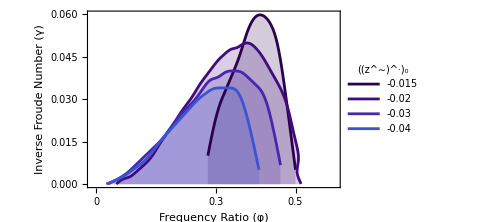

```mathematica
colors=Table[ColorData["DeepSeaColors",i],{i,0,1,1/6}];
ListLinePlot[{ldev1P,ldev2P,ldev25P,ldev3P},InterpolationOrder->2,Filling->Axis,PlotStyle->colors,FrameLabel->{{"Inverse Froude Number (γ)",None},{"Frequency Ratio (φ)",None}},PlotRange->{{-0.01,0.6},{-0,0.06}},Frame->True,PlotLegends->LineLegend[Automatic,{"-0.015","-0.02","-0.03","-0.04","-0.05","-0.08"},LegendLabel->"((z^∼)^·)_0"],FrameTicks->{{Automatic,Automatic},{{{0,"0",0.02},{0.1,"0.1",0.02},{0.5,"0.5",0.02},{0.2,"0.2",0.02},{0.3,"0.3",0.02},{0.4,"0.4",0.02}},Automatic}},ImageSize->Medium,LabelStyle->{Black,17}]
```

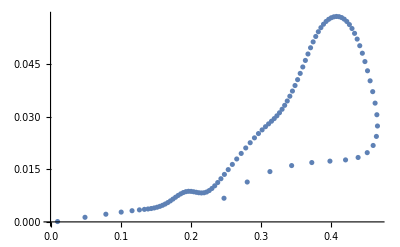

```mathematica
ListPlot[ldev1P]
processPoints[ldev2][[4]]
```